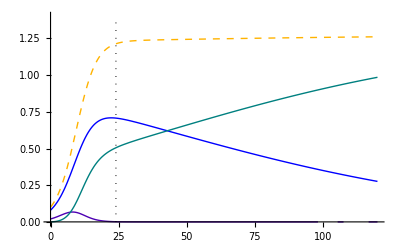

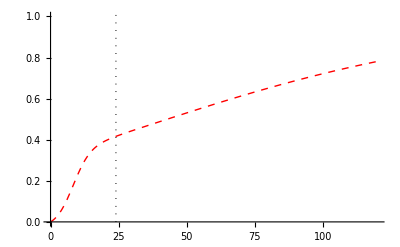

```mathematica
Clear[r1,r2,d1,d2,d3,k,Sol1]
r1=0.30;
r2=0.40;
d1=0.06;
d2=0.06;
d3=0.02;
k=0.5;
m=1.5;
eq1=n1'[t]==(r1(1-(n1[t]+n2[t]+n3[t])/m)-d1)n1[t];
eq2=n2'[t]==(r2(1-(n1[t]+n2[t]+n3[t])/m)-d2-d3) n2[t]-k n1[t] n2[t];
eq3=n3'[t]==(r2 (1-(n1[t]+n2[t]+n3[t])/m)-d2)n3[t]+k n1[t] n2[t];
inl1=n1[0]==0.08;
inl2=n2[0]==0.02;
inl3=n3[0]==0;
Sol1=NDSolve[{eq1,eq2,eq3,inl1,inl2,inl3},{n1,n2,n3},{t,0,300}];
n1[t]/.Sol1;
y1[t_]:=(n1[t]/.Sol1)[[1]];
y2[t_]:=(n2[t]/.Sol1)[[1]];
y3[t_]:=(n3[t]/.Sol1)[[1]];
p1=Plot[y1[t],{t,0,120},PlotRange->{0,1.4},PlotStyle->RGBColor[0,0,1]];
p2=Plot[y2[t],{t,0,120},PlotRange->{0,1.4},PlotStyle->RGBColor[0.3,0,0.7]];
p3=Plot[y3[t],{t,0,120},PlotRange->{0,1.4},PlotStyle->{RGBColor[0,0.5,0.5]}];
p4=Plot[(y1[t]+y2[t]+y3[t]),{t,0,120},PlotRange->{0,1.4},PlotStyle->{RGBColor[1,0.7,0],Dashed}];
p5=Plot[y3[t]/(y1[t]+y2[t]+y3[t]),{t,0,120},PlotRange->{0,1},PlotStyle->{Red,Thick,Dashed}];
p6=ParametricPlot[{24,m},{m,0,1.4},PlotStyle->{Black,Dotted}];
Show[p1,p2,p3,p4,p6,PlotRange->{0,1.4}]
Show[p5,p6,PlotRange->{0,1}]
ParametricPlot3D[{y1[t],y2[t],y3[t]},{t,0,300},AxesLabel->{"n1","n2","n3"},PlotRange->{0,1.4}]
```

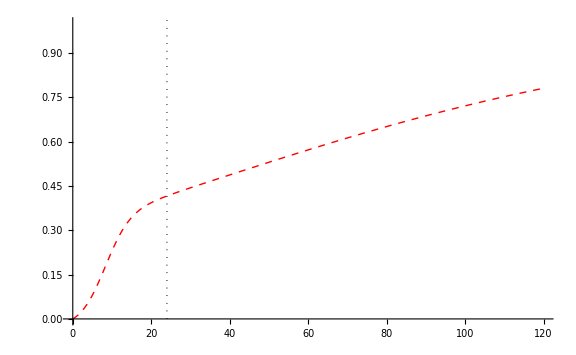

```mathematica
Show[%112,ImageSize->Large]
```

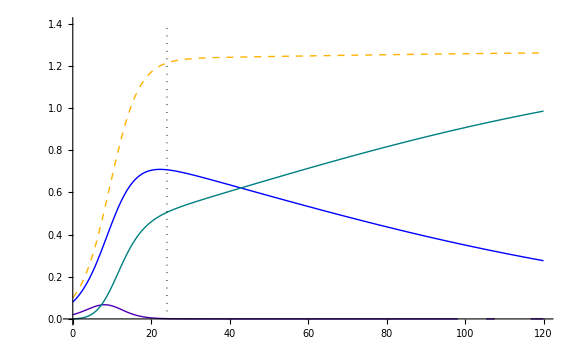

```mathematica
Show[%82,ImageSize->Large]
```

```mathematica
p11=ContourPlot3D[0==(r1(1-(n1+n2+n3)/m)-d1)n1,{n1,0,1.4},{n2,0,1.4},{n3,0,1.4},ColorFunction->Hue,Mesh->None,AxesLabel->{"n1","n2","n3"},ContourStyle->Opacity[0.6]]
p12=ContourPlot3D[0==(r2(1-(n1+n2+n3)/m)-d2-d3) n2-k n1 n2,{n1,0,1.4},{n2,0,1.4},{n3,0,1.4},ColorFunction->"Rainbow",Mesh->None,AxesLabel->{"n1","n2","n3"},ContourStyle->Opacity[0.6]]
p13=ContourPlot3D[0==(r2 (1-(n1+n2+n3)/m)-d2)n3+k n1 n2,{n1,-0.5,1.4},{n2,-0.5,1.4},{n3,-0.5,1.4},ColorFunction->"BlueGreenYellow",Mesh->None,AxesLabel->{"n1","n2","n3"},ContourStyle->Opacity[0.6]]
Show[p11,p12,p13]
NSolve[0==(r1(1-(n1+n2+n3)/m)-d1)n1&&0==(r2(1-(n1+n2+n3)/m)-d2-d3) n2-k n1 n2&&0==(r2 (1-(n1+n2+n3)/m)-d2)n3+k n1 n2,{n1,n2,n3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Clear[A,n1,n2,n3]
A=Array[f,{10,10}];
For[i=1,i<11,i++,
For[j=1,j<11,j++,
inl11=n1[0]==0.1*i;
inl21=n2[0]==0.1*j;
inl31=n3[0]==0;
Sol1=NDSolve[{eq1,eq2,eq3,inl11,inl21,inl31},{n1,n2,n3},{t,0,100}];
y1[t_]:=(n1[t]/.Sol1)[[1]];
y2[t_]:=(n2[t]/.Sol1)[[1]];
y3[t_]:=(n3[t]/.Sol1)[[1]];
f[i,j]=ParametricPlot3D[{y1[t],y2[t],y3[t]},{t,0,300},AxesLabel->{"n1","n2","n3"},PlotRange->{0,1.4}];
Clear[y1,y2,y3,Sol1,n1,n2,n3]
]]
Show[A]
```

-Graphics3D-

```mathematica
Show[%1835,ImageSize->Large]
```

-Graphics3D-

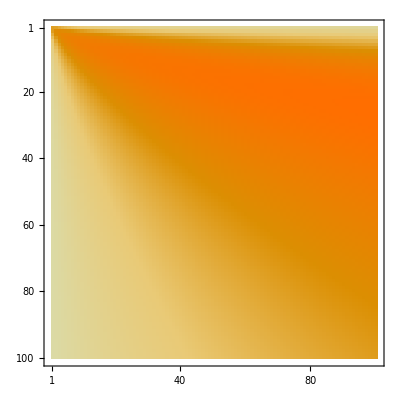

```mathematica
Clear[B]
B=Array[g,{100,100}];
For[i=1,i<101,i++,
For[j=1,j<101,j++,
inl12=n1[0]==0.01*i;
inl22=n2[0]==0.01*j;
inl32=n3[0]==0;
Sol1=NDSolve[{eq1,eq2,eq3,inl12,inl22,inl32},{n1,n2,n3},{t,0,100}];
y1[t_]:=(n1[t]/.Sol1)[[1]];
y2[t_]:=(n2[t]/.Sol1)[[1]];
y3[t_]:=(n3[t]/.Sol1)[[1]];
g[i,j]=y3[20]/(y1[20]+y2[20]+y3[20])
]]
ph=MatrixPlot[B]
```

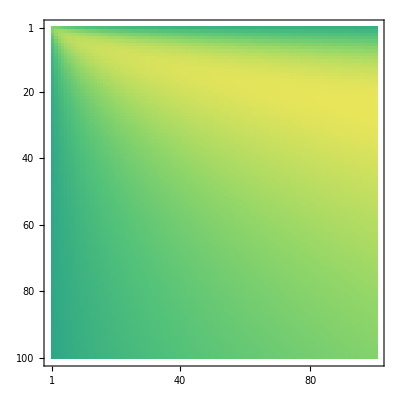

```mathematica
MatrixPlot[B,ColorFunction->"BlueGreenYellow"]
```

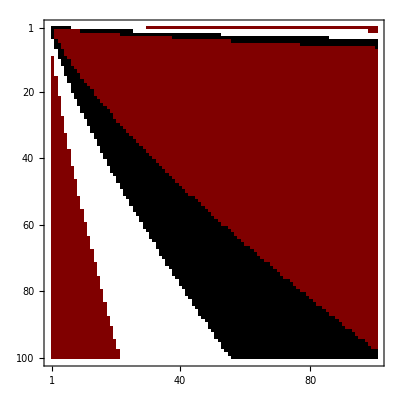

```mathematica
MatrixPlot[B,ColorFunction->(Which[0.6<#<0.7,RGBColor[1,1,1],0.7<#<0.8,RGBColor[0,0,0]]&)]
```

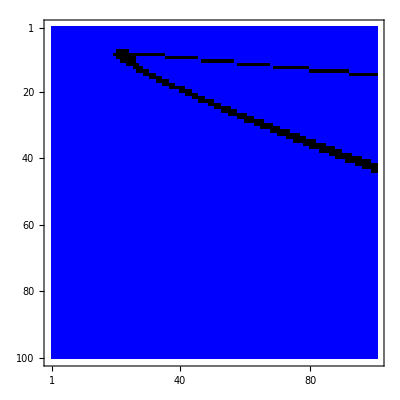

```mathematica
p11=MatrixPlot[B,ColorFunction->(RGBColor[#-0.15,0,1-#+0.15]&)];
p22=MatrixPlot[B,ColorFunction->(If[0.95<#<0.96,{Black,Opacity[0.1]},{Blue,Opacity[0]}]&)];
Show[p11,p22]
```

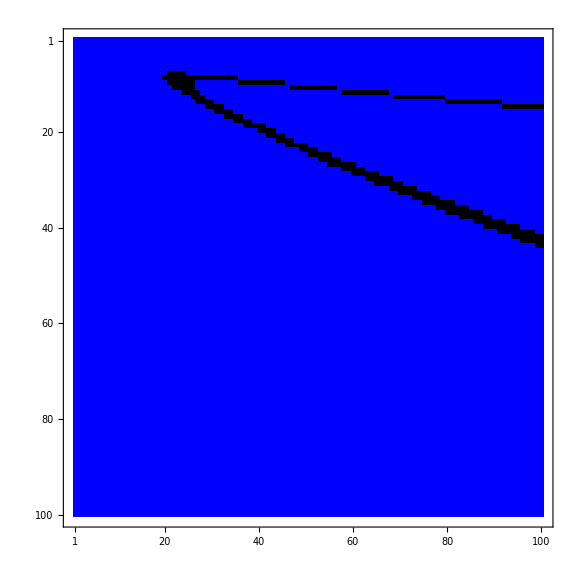

```mathematica
Show[%121,ImageSize->Large]
```

```mathematica
Clear[n,r,k,d,eq,inl,a]
eq=n'[t]==r n[t](1-n[t]/k)-d n[t];
DSolve[eq,n[t],t];
Reduce[{0.22252 k/r==1.19315,0.22252 k/(r 0.098)-1==11.23319}]
```

False

```mathematica
{{n(t)->-(k (r-d) ⅇ^(Subscript[c, 1] d k+r t))/(ⅇ^(Subscript[c, 1] k r+d t)-r ⅇ^(Subscript[c, 1] d k+r t))}}
```